```mathematica
ϵ={0.02,0.012,0.006}
```

{0.02,0.012,0.006}

```mathematica
ϵAve=(1/240000){0.0196*177236+0.0229*3497+0.0163*42999+0.013*7846+0.0097*3596,0.0156*6127+0.0131*140821+0.0105*69396+0.008*10925+0.0054*4840+0.00288*3229,0.0097*14015+0.0075*82657+0.0053*90168+0.0031*25549+0.000956*13185-0.00123*11321-0.0034*2873,
0.00715*2345+0.00535*9044+0.0035*159761+0.0017*40201-0.00003*17777-0.001834*10544,
0.00667*1129+0.004562*8315+0.00245*132434+0.000346*80970-0.0017616*16465(*,0.00479*2921+0.00334*14003+0.0018633*46488+0.00043*134718-0.001*33839-0.0024*6740*),-0.00193*137006-0.0017*36223-0.00146*17865-0.00123*11170-0.00099*9258-0.0007622*6746-0.00052*6722-0.00029*6223,-0.0039*130610-0.00337*38360-0.0028*18870-0.00233624*11879-0.00181*8979-0.00129*7111-0.00077*6758-0.00025*6063}
```

{0.0182986,0.0116326,0.00542449,0.00280328,0.00153724,-0.00160596,-0.00313077}

```mathematica
Nx={48604+18431+9709+4891+7231+4792,53305+18730+8333+2283+6386+2455,41715+8959+4439+2145+817,76740+26258+10976,
56098+41894+18373(*,87411+70620+23242*),0,0}
Ny={49192+21325+7317+26507+11947+6149,79793+13661+6420+3454+6304+3315,46995+15707+6643+2208+1239,0,3579(*,11341*),0,0}
Nz={0,0,31715+4366+47349+801+5236+174,62875+5248+167+34534+207+5180,72433+8814+9489+2278+159+3454+1555(*,1792+5284+2060+4628+816+1661*),212533+22639,185965+42320}
```

{93658,91492,58075,113974,116365,0,0}

{122437,112947,72792,0,3579,0,0}

{0,0,89641,108211,98182,235172,228285}

```mathematica
plotFont={FontWeight->"Bold",FontSize->12};
```

```mathematica
u=ListPlot[Table[{ϵAve[[k]]*100,Nx[[k]]/240000.+Ny[[k]]/240000.},{k,1,7}],AxesOrigin->{-1,0},AxesLabel->{"ϵ (%)","ϕ"},BaseStyle->plotFont,PlotRange->{-0.1,1.1},PlotStyle->Blue,ImageSize->800];
```

```mathematica
t=ListPlot[Table[{ϵAve[[k]]*100,Nz[[k]]/240000.},{k,1,7}],AxesOrigin->{-1,0},AxesLabel->{"ϵ (%)","ϕ"},PlotRange->{-0.1,1.1},PlotStyle->Orange];
```

```mathematica
Fit[Table[{ϵAve[[k]]*100,Nx[[k]]/240000.+Ny[[k]]/240000.},{k,1,7}],{1,x,x^2,x^3,x^4},x]
```

0.273787+0.836676 x-0.578586 x^2+0.35767 x^3-0.103172 x^4

```mathematica
Fit[Table[{ϵAve[[k]]*100,Nz[[k]]/240000.},{k,1,7}],{1,x,x^2,x^3,x^4},x]
```

0.669232-0.895423 x+0.580712 x^2-0.41374 x^3+0.13893 x^4

```mathematica
v=Plot[0.2737865425846048+0.8366764453073986 x-0.5785855352673751 x^2+0.3576698823542988 x^3-0.10317153583381446 x^4,{x,-0.6,2}];
```

```mathematica
s=Plot[0.6692323552664103-0.8954231587167464 x+0.5807119152941623 x^2-0.41373990649192893 x^3+0.13892954905864366 x^4,{x,-2,1.3},PlotStyle->Red];
```

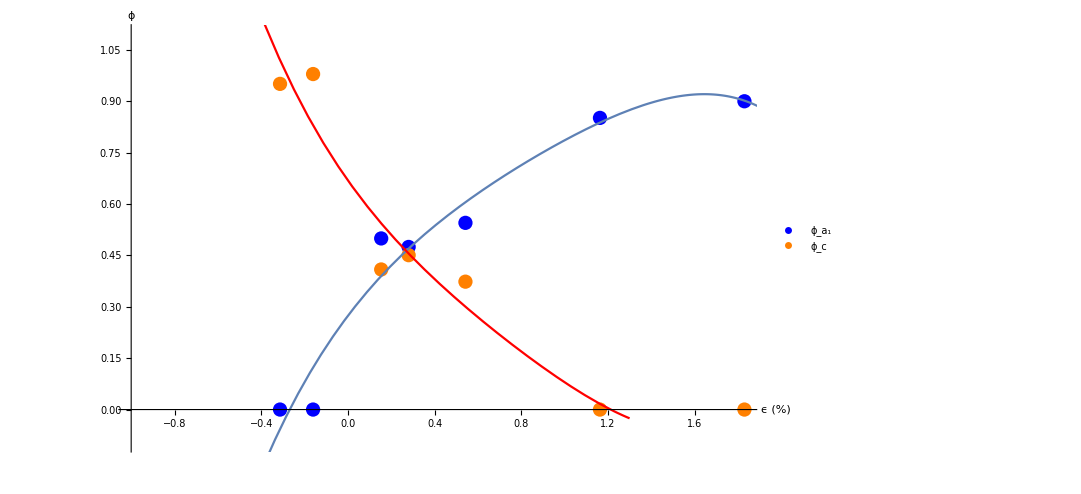

```mathematica
Legended[Show[{u,t,v,s}],Placed[PointLegend[{Blue,Orange},{"ϕ_a_1","ϕ_c"}],Right]]
```